## Explore transition terms between road segments

We want cars to transition faster when there are more cars, but only up to a point, as congestion then slows them down.

```mathematica
plotmin=-5;plotmax=40;
```

## Quadratic

A standard “carrying capacity” term is simple and has the desired effect.

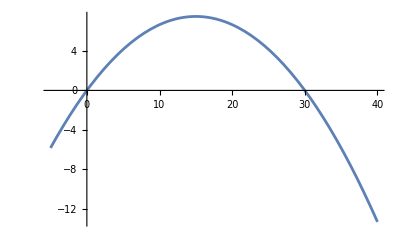

```mathematica
capacity=30;
quadratic[r_]=r (1-r/capacity);
Plot[quadratic[r],{r,plotmin,plotmax}]
```

## Sum of sigmoids

However, if other terms push the number of cars in a road segment r(t) beyond its carrying capacity, the sign of the quadratic term switches, meaning that cars begin going the opposite direction.

We would like the transition rate to decrease when the road gets congested, but only to a point. We would like the transition to asymptotically approach a minimum nonzero rate. Sigmoid functions provide this behavior.

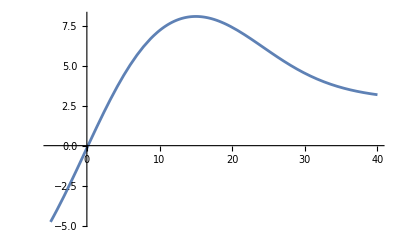

```mathematica
σ[x_]=LogisticSigmoid[x];c=3/8;
transition1[r_]=a σ[4/a r]-a/2;
transition2[r_]=-c a σ[4/a(r-a)];
capacity=15;
sigmoidsUnsolved[r_]=transition1[r]+transition2[r];
minimizer=Solve[sigmoidsUnsolved'[r]==0,r,Reals][[1,1,2]];
asol=Solve[minimizer==capacity,a][[1,1]];

sigmoids[r_]=sigmoidsUnsolved[r]/.asol;

Plot[sigmoids[r],{r,plotmin,plotmax}]
```

## Piecewise

Unfortunately, the sigmoid function is not dimensionally homogeneous. We attempt a piecewise function that is dimensionally homogeneous and has the other desired properties. We choose the minimum rate b and the “carrying capacity” c in the quadratic term, then solve for the other coefficients to make the piecewise function C^1.

### C^1 piecewise

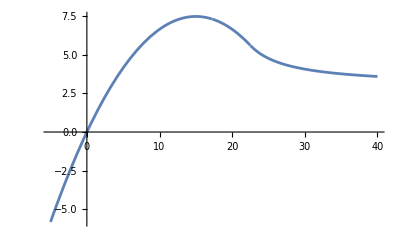

```mathematica
b=-3;capacity=30;
before[r_]:=r(1-r/capacity);
after[r_]:=d/(r-a)-b;
switchtime=3/4 capacity;
sol=Solve[{before[z]==after[z],before'[z]==after'[z]},{a,d}][[1]];

piecewise[r_]:=before[r]Boole[r<=switchtime]+after[r]Boole[switchtime<r]/.(sol/.z->switchtime);

Plot[piecewise[r],{r,plotmin,plotmax}]
```

### C^2 piecewise

Not possible with this form of function because quadratic has positive second derivative and 1/x has negative second derivative.

## Comparison

```mathematica
plot=Plot[{quadratic[r],sigmoids[r],piecewise[r]},{r,plotmin,plotmax},
PlotLabels->{quadratic,sigmoids,piecewise}]
```

-Graphics-

```mathematica
folder="evolution-transition-comparison/";
multidat=Cases[First@plot,Line[data_]:>data,-4];
Export[folder<>IntegerString[#2]<>".txt",#,"CSV"]&~MapIndexed~multidat;
```